# Double Pendulum

We shall consider the double pendulum, where two masses are attached together in series to a pivot point by rigid massless rods.
The masses are further constrained to move in a two dimensional plane.

## Energy

Let’s set up our potential and kinetic energy terms, so that we can build the total energy and Lagrangian,

```mathematica
U=-(m1+m2)g l1 Cos[θ1[t]]-m2 g l2 Cos[θ2[t]]+m1 g l1+m2 g l1+m2 g l2;
T=1/2(m1+m2) l1^2 θ1'[t]^2+1/2 m2 l2^2 θ2'[t]^2+m2 l1 l2 θ1'[t]θ2'[t]Cos[θ1[t]-θ2[t]];
L=T-U;
EE=T+U;
```

From here we can build the Euler-Lagrange Equations,
d/dt(∂L)/(∂θ̇)==(∂L)/(∂θ)
The left hand side will contain the highest order time derivatives, which we can solve for to return equations of motion.
If we re-write the first derivatives as their own variables, we can write the Equations of Motion in NDSolve-able form.

```mathematica
D[{D[L,θ1'[t]],D[L,θ2'[t]]},t]=={D[L,θ1[t]],D[L,θ2[t]]}//FullSimplify;
Solve[%,{θ1''[t],θ2''[t]}][[1]];
%/.{ θ1'[t]->θ1dot[t], θ2'[t]->θ2dot[t]};
equationsOfMotion={
θ1dot'[t]==θ1''[t],
θ2dot'[t]==θ2''[t],
θ1'[t]==θ1dot[t],
θ2'[t]==θ2dot[t]
}/.%;
```

We’ll solve this system for the case where m_1==m_2 and l_1==l_2. In this case, if we non-dimensionalise, since θ_1 and θ_2 are both angles these are already dimensionless, we can extract an energy constant proportional to U_0=m g l and a time constant that will be proportional to ω_0^-1==√(l/g), using this as the time constant, and recasting OverDot[θ_i]->√(l/g)OverDot[θ_i], is equivalent to setting m=g=l=1. This choice gives potential energies in the range 0–6. We can solve and animate the solution. For the system in equilibrium position with OverDot[θ_2]=0, the first angular velocity can be written as a function of the total energy, OverDot[θ_2]=√E.

```mathematica
initialConditions={
θ1[0]==0,
θ2[0]==0,
θ1dot[0]==√2,
θ2dot[0]==0
};
assumptions={l1->1,l2->1,m1->1,m2->1,g->1};
solution=NDSolve[{
equationsOfMotion/.assumptions,
initialConditions
},{θ1,θ1dot,θ2,θ2dot},{t,0,1000}];
Animate[ParametricPlot[{
{Sin[θ1[t]],-Cos[θ1[t]]}s,
{Sin[θ1[t]],-Cos[θ1[t]]}+{Sin[θ2[t]],-Cos[θ2[t]]}s
}/.solution,{s,0,1},PlotRange->{{-2.1,2.1},{-2.1,2.1}},Epilog->({PointSize[Large], Point[{0,0}],Point[{Sin[θ1[t]],-Cos[θ1[t]]}],Point[{Sin[θ1[t]],-Cos[θ1[t]]}+{Sin[θ2[t]],-Cos[θ2[t]]}]}/.solution[[1]])],{t,0,100},AnimationRate->2
]
```

## Analysis

We can do the usual analysis of this system, which will start out by finding fixed points.
Note these are all stationary (velocities zero) as you might expect, so zero kinetic energy.
We can evaluate the potential energy at each point too and see a ladder of equally spaced energies.

```mathematica
equationsOfMotion/.assumptions/.{θ1'[t]->0,θ2'[t]->0,θ1dot'[t]->0,θ2dot'[t]->0};
Solve[%,{θ1[t],θ2[t],θ1dot[t],θ2dot[t]}]
Normal[%]/.{C[1]->0,C[2]->0}
U/.assumptions/.%
```

{{θ1dot[t]→0,θ2dot[t]→0,θ1[t]→ConditionalExpression[2 π C[1], C[1]∈ℤ],θ2[t]→ConditionalExpression[-2 π C[2], C[2]∈ℤ]},{θ1dot[t]→0,θ2dot[t]→0,θ1[t]→ConditionalExpression[2 π C[1], C[1]∈ℤ],θ2[t]→ConditionalExpression[-π-2 π C[2], C[2]∈ℤ]},{θ1dot[t]→0,θ2dot[t]→0,θ1[t]→ConditionalExpression[π+2 π C[1], C[1]∈ℤ],θ2[t]→ConditionalExpression[-2 π C[2], C[2]∈ℤ]},{θ1dot[t]→0,θ2dot[t]→0,θ1[t]→ConditionalExpression[π+2 π C[1], C[1]∈ℤ],θ2[t]→ConditionalExpression[-π-2 π C[2], C[2]∈ℤ]}}

{{θ1dot[t]→0,θ2dot[t]→0,θ1[t]→0,θ2[t]→0},{θ1dot[t]→0,θ2dot[t]→0,θ1[t]→0,θ2[t]→-π},{θ1dot[t]→0,θ2dot[t]→0,θ1[t]→π,θ2[t]→0},{θ1dot[t]→0,θ2dot[t]→0,θ1[t]→π,θ2[t]→-π}}

{0,2,4,6}

We can evaluate the Jacobian of the equations of motion to characterise each fixed point. Let’s look at the zero potential energy point first.

```mathematica
Map[Last,equationsOfMotion/.assumptions];(*This Map gives us f as a function rather than an equation set*)
Grad[%,{θ1dot[t],θ2dot[t],θ1[t],θ2[t]}];
%/.{θ1dot[t]->0,θ2dot[t]->0,θ1[t]->0,θ2[t]->0};
%//MatrixForm
Eigenvalues[%%]
```

(0 | 0 | -2 | 1
0 | 0 | 2 | -2
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

{ⅈ √(2+√2),-ⅈ √(2+√2),ⅈ √(2-√2),-ⅈ √(2-√2)}

There are two pairs of imaginary eigenvalues, ±ⅈ √(2+√2), and ±ⅈ √(2-√2), corresponding to a fast and a slow oscillation with frequencies ω_+=√(2+√2) and ω_-=√(2-√2). In principle, you can look at the eigenvectors to determine which is the oscillation and which is the translation mode by comparing the relative signs of the position components.

## Poincaré Maps

As a four dimensional system, it can be difficult to get insights about this system. One method to get a handle on this is the Poincaré map. First, since there is a conserved quantity in total energy, if you know three of the variables, the other can be recovered, reducing the set of variables to three needed to describe the system. The next part is to consider when the 3-D trajectory crosses a surface and log those crossing points. E.g, for the double pendulum, if we know (θ̇)_1, (θ̇)_2, and θ_1-θ_2 for a fixed energy then we can reconstruct all the variables of the system. Further, if we log when the pendulum straightens out, when θ_1-θ_2=0 then we can plot the velocities for which that happens. This changes our representation from a continuous curve in a higher dimension to a set of discrete of discrete points in a lower dimension.

-Graphics3D-

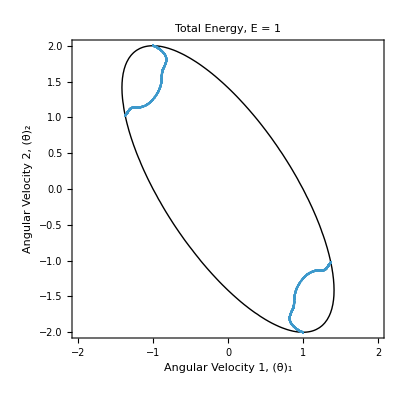

```mathematica
energy=1;
initialConditions={
θ1[0]==0,
θ2[0]==0,
θ1dot[0]==√energy,
θ2dot[0]==-2 √energy
};
{solution,events}=Reap@NDSolve[{
equationsOfMotion/.{l1->1,l2->1,m1->1,m2->1,g->1},
initialConditions,
WhenEvent[θ1[t]==θ2[t],{Sow[{θ1[t],θ1dot[t],θ2[t],θ2dot[t]}]}]
},{θ1,θ1dot,θ2,θ2dot},{t,0,10000}];
Show[
ParametricPlot3D[{θ1dot[t],θ2dot[t],Sin[θ1[t]-θ2[t]]}/.solution,{t,0,100},PlotRange->{{-3,3},{-3,3},Automatic},AxesLabel->{"(θ̇)_1", "(θ̇)_2", "Sin[θ_1-θ_2]"}],
Plot3D[0,{x,-3,3},{y,-3,3},Mesh->None,PlotStyle->Opacity[0.5]]
]
Show[
ContourPlot[θ1dot^2+θ1dot θ2dot+1/2 θ2dot^2==energy,{θ1dot,-2 √energy,2 √energy},{θ2dot,-2 √energy,2 √energy},ContourStyle->{Black,Thin},PlotLabel->("Total Energy, E = "<>ToString[energy]),FrameLabel->{"Angular Velocity 1, (θ̇)_1", "Angular Velocity 2, (θ̇)_2"}],
ListPlot[Map[{#[[2]],#[[4]]}&,events[[1]]],AspectRatio->1]
]
```

If we increase the energy, we can see the trajectories changing from closed orbits to a chaotic pattern were the orbits smear and fill space.

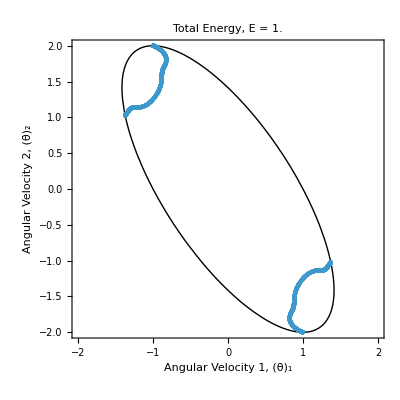
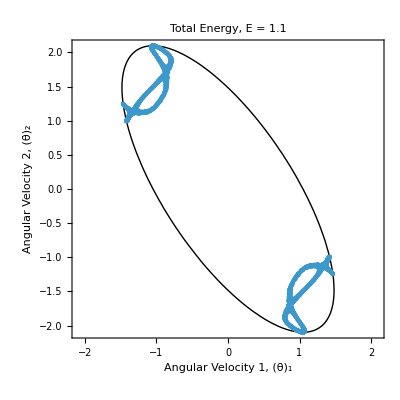
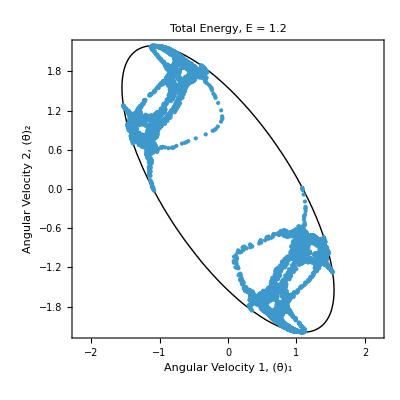
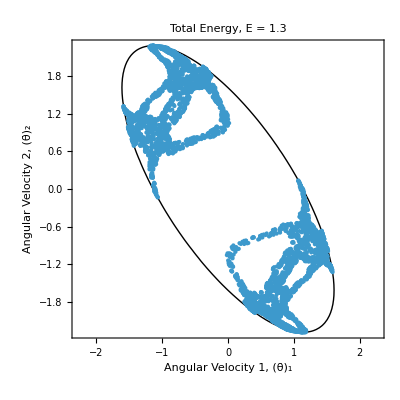
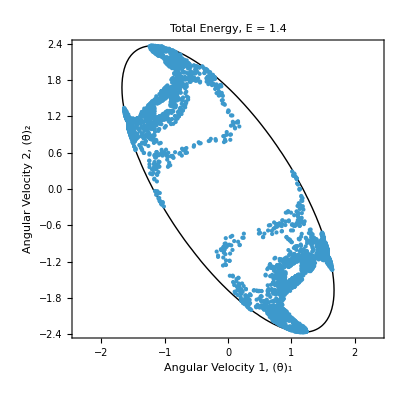
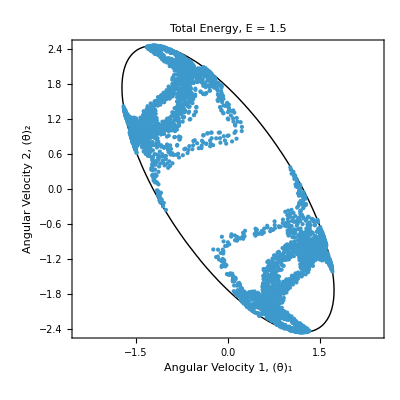
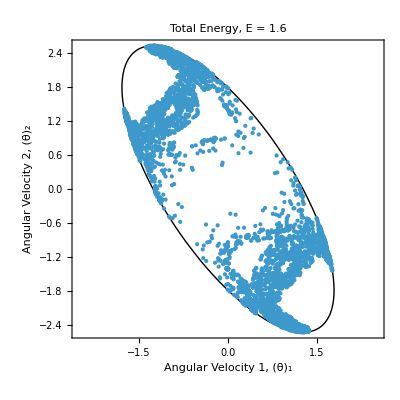
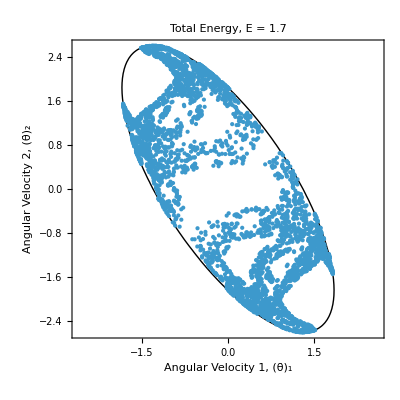

```mathematica
Table[Module[
{initialConditions,solution,events},
initialConditions={
θ1[0]==0,
θ2[0]==0,
θ1dot[0]==√energy,
θ2dot[0]==-2 √energy
};
{solution,events}=Reap@NDSolve[{
equationsOfMotion/.{l1->1,l2->1,m1->1,m2->1,g->1},
initialConditions,
WhenEvent[θ1[t]==θ2[t],{Sow[{θ1[t],θ1dot[t],θ2[t],θ2dot[t]}]}]
},{θ1,θ1dot,θ2,θ2dot},{t,0,10000}];
Show[
ContourPlot[θ1dot^2+θ1dot θ2dot+1/2 θ2dot^2==energy,{θ1dot,-2 √energy,2 √energy},{θ2dot,-2 √energy,2 √energy},ContourStyle->{Black,Thin},PlotLabel->("Total Energy, E = "<>ToString[energy]),FrameLabel->{"Angular Velocity 1, (θ̇)_1", "Angular Velocity 2, (θ̇)_2"}],
ListPlot[Map[{#[[2]],#[[4]]}&,events[[1]]],AspectRatio->1,PlotStyle->PointSize[Tiny]]
]],{energy,1,2,0.1}]
```